```mathematica
Integrate[(1+x/4)*Exp[-x^2/2-x^(1/2)],{x,0,Infinity}]
```

1/96 (-48 2^(3/4) Gamma[3/4] HypergeometricPFQ[{},{1/2,5/4},1/128]+6 √(2 π) (8 HypergeometricPFQ[{},{1/4,3/4},1/128]+HypergeometricPFQ[{},{3/4,5/4},1/128])-3 2^(3/4) Gamma[3/4] HypergeometricPFQ[{},{5/4,3/2},1/128]-8 2^(1/4) Gamma[5/4] (3 HypergeometricPFQ[{},{1/2,3/4},1/128]+2 HypergeometricPFQ[{},{3/2,7/4},1/128])+24 HypergeometricPFQ[{1},{1/4,1/2,3/4},1/128]+48 HypergeometricPFQ[{1},{3/4,5/4,3/2},1/128])

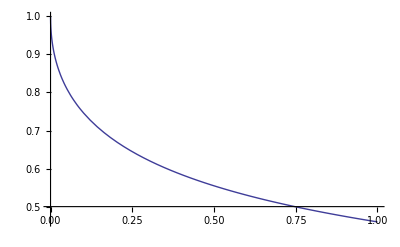

```mathematica
w[s_,a_] = (1+s/(4*a))*Exp[-Sqrt[s/a]];
Plot[w[z,1],{z,0,1}]
```

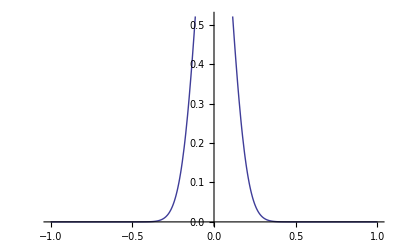

```mathematica
n[s_,a_] = Exp[-s^2/(2*a^2)];
Plot[n[z,0.1],{z,-1,1}]
```

```mathematica
dw = D[w[z,1],z]
```

ⅇ^(-√z)/4-(ⅇ^(-√z) (1+z/4))/(2 √z)

```mathematica
Integrate[Exp[-x^4-x],{x,0,Infinity}]
```

1/24 (24 Gamma[5/4] HypergeometricPFQ[{},{1/2,3/4},1/256]-6 √π HypergeometricPFQ[{},{3/4,5/4},1/256]+3 Gamma[3/4] HypergeometricPFQ[{},{5/4,3/2},1/256]-HypergeometricPFQ[{1},{5/4,3/2,7/4},1/256])

```mathematica
D[(1+x/4)*Exp[-x^(1/2)],{x,3}]
```

3/4 (ⅇ^(-√x)/(4 x^(3/2))+ⅇ^(-√x)/(4 x))+(-(3 ⅇ^(-√x))/(8 x^(5/2))-(3 ⅇ^(-√x))/(8 x^2)-ⅇ^(-√x)/(8 x^(3/2))) (1+x/4)

```mathematica
Series[(1+x/(4*a))*Exp[-Sqrt[x/a]],{x,0,5}]
```

1-√(1/a) √x+(3 x)/(4 a)-5/12 (1/a)^(3/2) x^(3/2)+x^2/(6 a^2)-1/20 (1/a)^(5/2) x^(5/2)+(17 x^3)/(1440 a^3)-(23 (1/a)^(7/2) x^(7/2))/10080+x^4/(2688 a^4)-(19 (1/a)^(9/2) x^(9/2))/362880+(47 x^5)/(7257600 a^5)+O[x]^(11/2)

```mathematica
Integrate[x^(5/2)*Exp[-x^2],{x,0,Infinity}]
```

1/2 Gamma[7/4]

```mathematica
Integrate[w[zz,1]*n[zz,1],{zz,-Infinity,z}]
```

$Aborted

```mathematica
c[σ_]=σ*Integrate[σ^-2*zz*w[zz,435]*n[zz,σ],{zz,0,+Infinity}]
```

ConditionalExpression[σ (1/870 √(π/2) (1/σ^2)^(3/2) σ^4 HypergeometricPFQ[{},{3/4,5/4},σ^2/24220800]+HypergeometricPFQ[{1},{1/4,1/2,3/4},σ^2/24220800]+(√(π/2) (1/σ^2)^(3/2) σ^4 HypergeometricPFQ[{3/2},{1/4,1/2,3/4},σ^2/24220800])/1740-1/(3480 2^(1/4) √435)(1/σ^2)^(1/4) σ^2 Gamma[3/4] (2 HypergeometricPFQ[{},{5/4,3/2},σ^2/24220800]+3 HypergeometricPFQ[{7/4},{1/2,3/4,5/4},σ^2/24220800])+(σ^2 HypergeometricPFQ[{2},{3/4,5/4,3/2},σ^2/24220800])/756900-1/(908280 2^(3/4) √435)(1/σ^2)^(3/4) σ^2 Gamma[5/4] (1816560 HypergeometricPFQ[{},{1/2,3/4},σ^2/24220800]+σ^2 HypergeometricPFQ[{9/4},{5/4,3/2,7/4},σ^2/24220800])),Re[σ^2]>0]

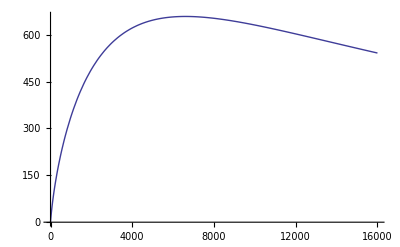

```mathematica
Plot[c[x],{x,1,16000},PlotRange->All]
```

```mathematica
V[z_,σ_]=Integrate[n[z-zz,σ]*w[zz,435],{zz,0,Infinity}];
```

```mathematica
Plot[V[z,50],{z,-200,200}]
```

$Aborted

```mathematica
nn[s_,sint_,a_] = Exp[-(s-sint)^2/(2*a^2)];
integrand[z_,zz_] = nn[z,zz,50]*w[zz,435];
```

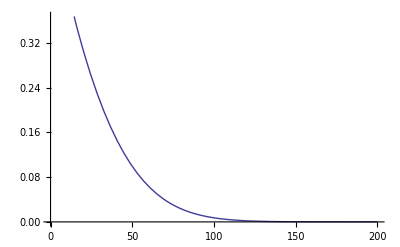

```mathematica
Plot[integrand[-50,x],{x,0,200}]
```

```mathematica
Integrate[integrand[z,x],{x,0,Infinity}]
```

∫_0^∞ ⅇ^(-(√x)/(√435)-(-x+z)^2/5000) (1+x/1740)ⅆx